```mathematica
With[
{colors=4},
TableForm[Table[
With[{good=Length[Select[ListofVars[FindFullFormula[VertexAdd[CompleteGraph[colors],Range[colors+1,n]]]],StringCount[SymbolName[#],"x"]+1==colors&]]},
{
n,
a StirlingS2[n-1,colors]-b StirlingS2[n-2,colors]+c StirlingS2[n-3,colors] == StirlingS2[n,colors ]-good,
good,
 StirlingS2[n,colors ]-good
}
],{n,colors,10}
], TableHeadings->{None, {"n","formula","good","bad"}}]
]
```

n | formula | good | bad
4 | True | 1 | 0
5 | a==6 | 4 | 6
6 | 10 a-b==49 | 16 | 49
7 | 65 a-10 b+c==286 | 64 | 286
8 | 350 a-65 b+10 c==1445 | 256 | 1445
9 | 1701 a-350 b+65 c==6746 | 1024 | 6746
10 | 7770 a-1701 b+350 c==30009 | 4096 | 30009

```mathematica
Table[
Labeled[
TableForm[
Table[
With[
{good=Length[Select[ListofVars[FindFullFormula[VertexAdd[CompleteGraph[colors+1],Range[colors+2,n]]]],StringCount[SymbolName[#],"x"]+1==colors&]]},

{
n,
StirlingS2[n,colors ],
StirlingS2[n,colors ]-Sum[ StirlingS1[colors,colors-k]*StirlingS2[n-k,colors],{k,0,colors-1}],
StirlingS2[n,colors ]-good,
good
}
]
,{n,colors-1,4}
], TableHeadings->{None, {"n","all","formula","computed bad","computed good"}}]
,
Style[colors,20,Red,Bold]
]
,{colors,2,5}
]
```

{n | all | formula | computed bad | computed good
1 | 0 | 0 | 0 | 0
2 | 1 | 0 | 1 | 0
3 | 3 | 1 | 3 | 0
4 | 7 | 3 | 7 | 02,n | all | formula | computed bad | computed good
2 | 0 | 0 | 0 | 0
3 | 1 | 0 | 1 | 0
4 | 6 | 3 | 6 | 03,n | all | formula | computed bad | computed good
3 | 0 | 0 | 0 | 0
4 | 1 | 0 | 1 | 04,n | all | formula | computed bad | computed good
4 | 0 | 0 | 0 | 05}

```mathematica
Table[
Labeled[
TableForm[
Table[
With[
{good=Length[Select[ListofVars[FindFullFormula[VertexAdd[CompleteGraph[colors+1],Range[colors+2,n]]]],StringCount[SymbolName[#],"x"]+1==colors&]]},

{
n,
StirlingS2[n,colors ],
Sum[ StirlingS1[colors,colors-k]*StirlingS2[n-k,n-colors],{k,0,colors-1}],
StirlingS2[n,colors ]-good,
good
}
]
,{n,colors,colors+5}
], TableHeadings->{None, {"n","all","formula","computed bad","computed good"}}]
,
Style[colors,20,Red,Bold]
]
,{colors,3,5}
]
```

{n | all | formula | computed bad | computed good
3 | 1 | 0 | 1 | 0
4 | 6 | 0 | 6 | 0
5 | 25 | 0 | 25 | 0
6 | 90 | 27 | 90 | 0
7 | 301 | 175 | 301 | 0
8 | 966 | 660 | 966 | 03,n | all | formula | computed bad | computed good
4 | 1 | 0 | 1 | 0
5 | 10 | 0 | 10 | 0
6 | 65 | 0 | 65 | 0
7 | 350 | 0 | 350 | 0
8 | 1701 | 256 | 1701 | 0
9 | 7770 | 2101 | 7770 | 04,n | all | formula | computed bad | computed good
5 | 1 | 0 | 1 | 0
6 | 15 | 0 | 15 | 0
7 | 140 | 0 | 140 | 0
8 | 1050 | 0 | 1050 | 0
9 | 6951 | 0 | 6951 | 0
10 | 42525 | 3125 | 42525 | 05}

```mathematica
MakeBoxes[StirlingS2[n_,k_],StandardForm]:=RowBox[{"{",GridBox[{{ToString[TraditionalForm[n]]},{ToString[TraditionalForm[k]]}},AutoDelete->False,GridBoxItemSize->{"Columns"->{{Automatic}},"Rows"->{{Automatic}}}],"}"}]
```

```mathematica
StandardForm[Sum[ StirlingS1[colors,colors-k]*StirlingS2[n-k,colors-1],{k,0,colors}]]
```

∑_(k=0)^colors [colors
colors-k] {n-k
colors-1}

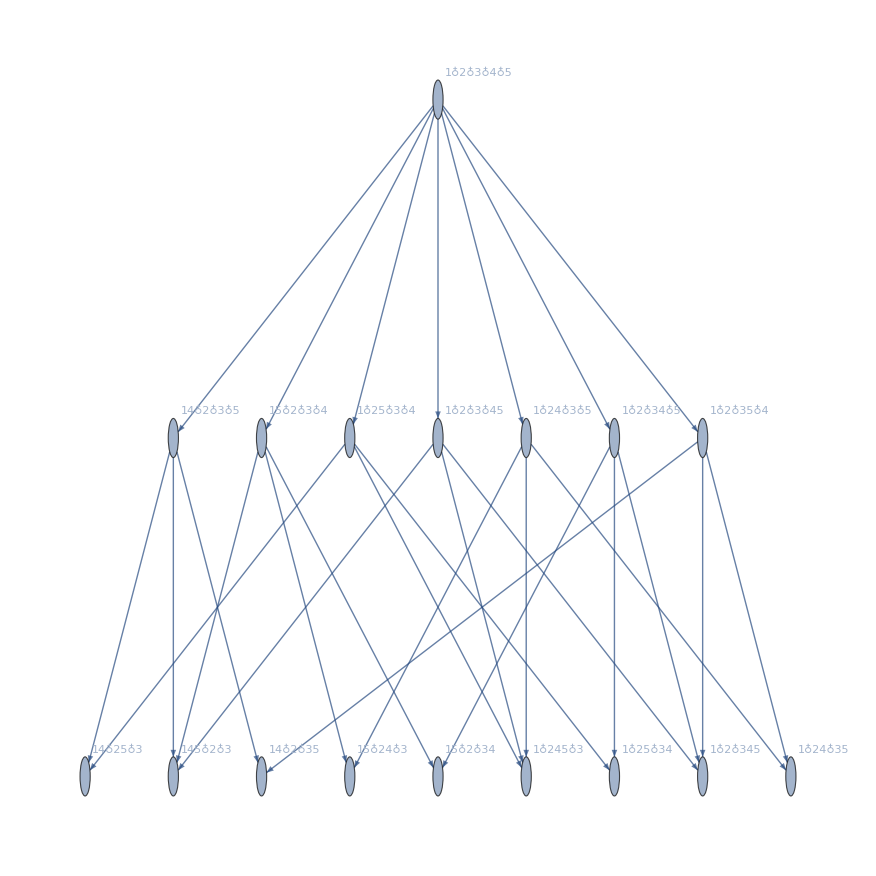

```mathematica
With[
{colors=2,n=5},
FormulaGraph[FindFullFormula[VertexAdd[CompleteGraph[colors+1],Range[colors+2,n]]]]
]
```

```mathematica
With[{colors=4},Sum[ StirlingS1[colors,colors-k]*StirlingS2[n-k,colors-1],{k,0,colors-1}]]
```

-6 {n-3
3}+11 {n-2
3}-6 {n-1
3}+{n
3}

```mathematica
With[{colors=5},Sum[ StirlingS1[colors,colors-k]*StirlingS2[n-k,colors-1],{k,0,colors-1}]]
```

24 {n-4
4}-50 {n-3
4}+35 {n-2
4}-10 {n-1
4}+{n
4}

```mathematica
With[{colors=4},
Table[
Sum[StirlingS1[colors,colors-k]*StirlingS2[n-k,n+1-colors],{k,0,colors-1}],
{n,colors+1,10}]//TableForm
]
```

0
0
64
369
1275
3410

```mathematica
Simplify[Sum[ StirlingS1[colors,colors-k]*StirlingS2[n-k,colors-1],{k,0,colors-1}]]
```

∑_(k=0)^(-1+colors) [colors
colors-k] {n-k
colors-1}

```mathematica
MatrixForm[
Table[
PadRight[Table[
StirlingS2[n,k],{k,0,n}],11]
,{n,0,10}
],
TableHeadings->{Map[Symbol["n"<>ToString[#]]&,Range[0,10]], Map[Symbol["k"<>ToString[#]]&,Range[0,10]]}
]
```

( | k0 | k1 | k2 | k3 | k4 | k5 | k6 | k7 | k8 | k9 | k10
n0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n2 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n3 | 0 | 1 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
n4 | 0 | 1 | 7 | 6 | 1 | 0 | 0 | 0 | 0 | 0 | 0
n5 | 0 | 1 | 15 | 25 | 10 | 1 | 0 | 0 | 0 | 0 | 0
n6 | 0 | 1 | 31 | 90 | 65 | 15 | 1 | 0 | 0 | 0 | 0
n7 | 0 | 1 | 63 | 301 | 350 | 140 | 21 | 1 | 0 | 0 | 0
n8 | 0 | 1 | 127 | 966 | 1701 | 1050 | 266 | 28 | 1 | 0 | 0
n9 | 0 | 1 | 255 | 3025 | 7770 | 6951 | 2646 | 462 | 36 | 1 | 0
n10 | 0 | 1 | 511 | 9330 | 34105 | 42525 | 22827 | 5880 | 750 | 45 | 1)

```mathematica
StirlingS2[6,4]
```

65

```mathematica
StirlingS2[5,5+1-4]
```

15

```mathematica
StirlingS2[6,6+1-4]
```

90

```mathematica
Export["D:\\K4.png",MobiusGraph5[K4Key,allGraphs4]]
```

D:\K4.png

```mathematica
Export["D:\\K5.png",Graph[MobiusGraph5[K5Key,allGraphs5],ImageSize->2000],ImageResolution->600]
```

D:\K5.png

```mathematica
Export["D:\\K5.svg",Graph[MobiusGraph5[K5Key,allGraphs5],ImageSize->2000],ImageResolution->600]
```

D:\K5.svg

```mathematica
MobiusGraph6[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofourrealnull"], vars, blocks=Association[],c,edges,set, found=Association[],nodeCount=Length[Flatten[allGraphs[key,"vertexsets"]]],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==1&]],problemSize=Length[allGraphs[0,"vertexsets"]]},
vars=ListofVars[form];

(* initialize all blocks to empty sets *)
Table[blocks[k]={},{k,0,problemSize}];
(* put each base set ion a bucket by length.  In eahc bucket we store the variable and the vertexsets associated with that variable *)
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofourrealnull"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}
];
(* now compute the edges.
For this we go over all blocks per size.
For each of the "size +1" we add and an edge if the first is a refinement of the second
*)
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],

AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,problemSize}];
Graph[vars,edges,VertexLabels->Table[n->Rotate[Style[SymbolToLabel2[n,nodeCount],40],Pi/6],{n,vars}],GraphLayout->"LayeredDigraphEmbedding"]
]
```

```mathematica
Export["D:\\K5.pdf",Graph[MobiusGraph6[K5Key,allGraphs5],ImageSize->2000,AspectRatio->1],ImageResolution->600]
```

D:\K5.pdf

```mathematica
MemoryInUse[]
```

2317981608

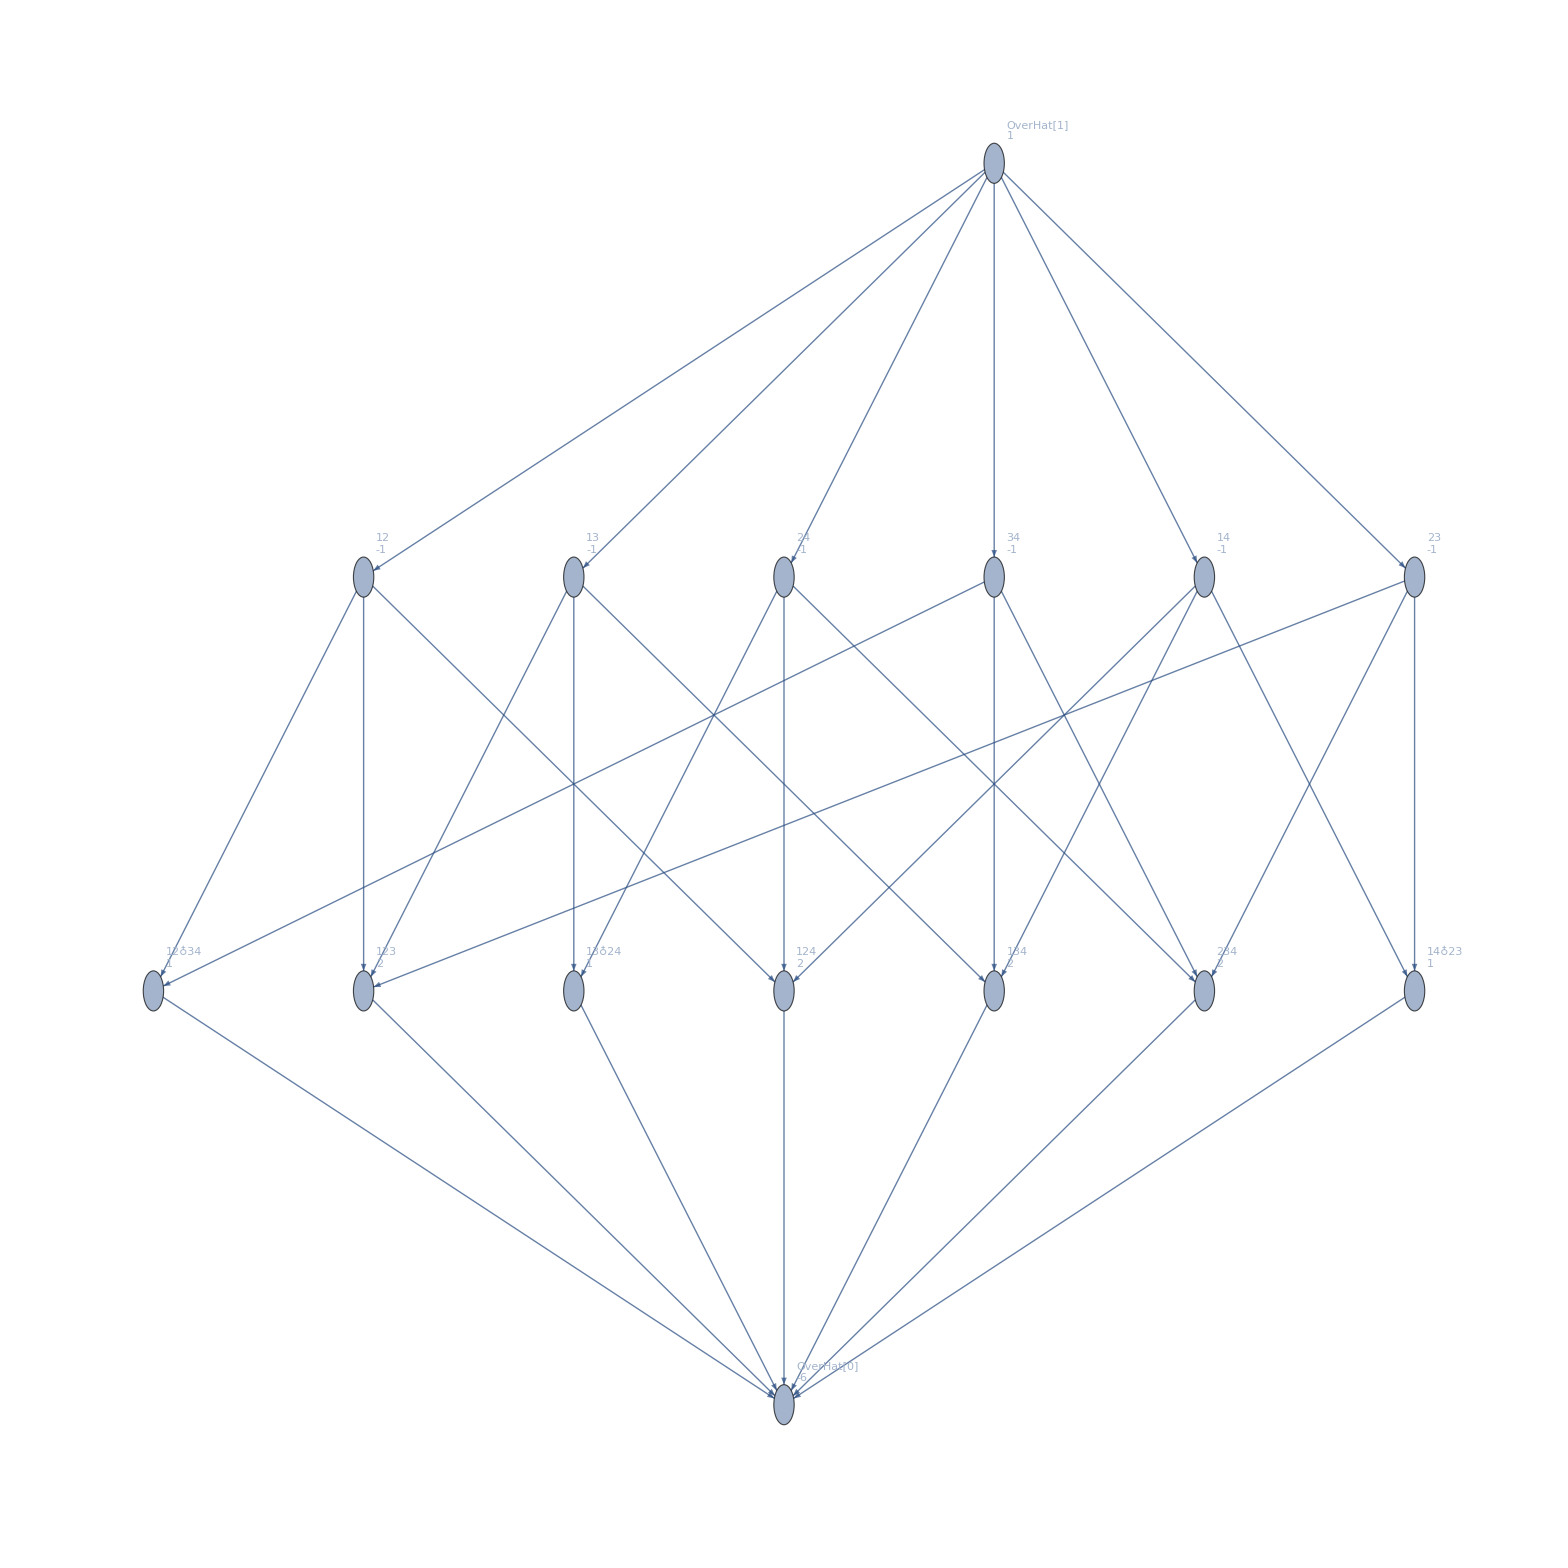

```mathematica
Graph[MobiusGraph5[K4Key,allGraphs4],ImageSize->2000,AspectRatio->1]
```

```mathematica
Export["D:\\K6.pdf",Graph[MobiusGraph5[K6Key,allGraphs6],ImageSize->2000],ImageResolution->600]
```

D:\K6.pdf

```mathematica
$HistoryLength=0
```

0

```mathematica
With[{colors=5},
Table[{Sum[ Style[StirlingS1[colors,colors-k],Red,20]*Style[StirlingS2[n-k,colors-1],Darker[Green],20],{k,1,colors}]==Sum[ StirlingS1[colors,colors-k]*StirlingS2[n-k,colors-1],{k,0,colors-1}]},{n,colors,10}]
]//TableForm
```

-50 0+0 0+-10 1+0 24+0 35==0
-50 0+0 0+-10 10+0 24+1 35==0
0 0+-50 1+0 24+10 35+-10 65==0
0 0+-50 10+1 24+35 65+-10 350==0
0 1+10 24+-50 65+35 350+-10 1701==0
0 10+24 65+-50 350+35 1701+-10 7770==0

```mathematica
Table[StirlingS2[n,4],{n,4,20}]
```

{1,10,65,350,1701,7770,34105,145750,611501,2532530,10391745,42355950,171798901,694337290,2798806985,11259666950,45232115901}